```mathematica
f[x_] = 2.7*ArcSin[2.22*x-1] - x +1.8
```

1.8-x-2.7 ArcSin[1-2.22 x]

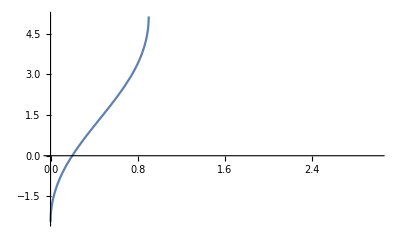

```mathematica
Plot[f[x],{x,-0,3}]
```

```mathematica
FindRoot[f[x],{x,0.1}]
```

```mathematica
{x->0.198686}
```

```mathematica
fi1[x_] = 2.7*ArcSin[2.22*x-1] +1.8
```

1.8-2.7 ArcSin[1-2.22 x]

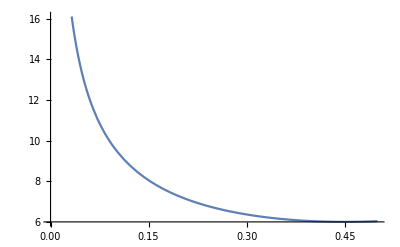

```mathematica
Plot[fi1'[x],{x,0,0.5}]
```

```mathematica
fi1'[0.198686]
```

7.22845

```mathematica
fi2[x_] = -(Sin[(1.8-x)/2.7]-1)/2.22
```

0.45045 (1-Sin[0.37037 (1.8-x)])

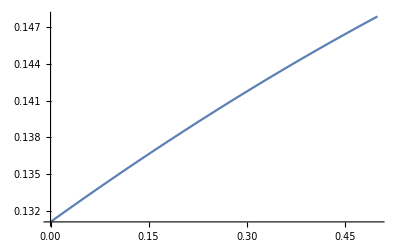

```mathematica
Plot[fi2'[x],{x,0,0.5}]
```

```mathematica
fi2'[0.198686]
```

0.138342